Saving directly beside this code file: G:\Thesis\Thesis done 2\Final Folder

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Parallel kernels active: 8

Computing RIS Ce,max from PATCH10 locked core...

RIS Ce diagnostics {Ne,K,CeBits,Last25Ratio,BadTerms}: {{1,0,1.66497,1.,0},{2,100,2.4506,1.65969015971×10^-22,0},{6,320,3.67436,7.87401053419×10^-23,0},{15,900,4.50031,2.09823592414×10^-25,0}}

Computing No-RIS Ce,max from PATCH1 locked core...

No-RIS Ce diagnostics {Ne,K,CeBits}: {{1,0,1.79641660634638119367551253455872983628234913},{2,80,2.39200554492799032034394213041696696065248435},{6,180,3.18778837380390622692446566970212794435374554},{15,360,3.69388272054335570725227743873931615832850195}}

Computing analytical comparison curves...

Computing small hollow MC validation markers...

Max absolute CF-MC error = 0.0143033 bits/s/Hz

RIS ESMC at 30 dB: {{1,12.7733},{2,11.9877},{6,10.7639},{15,9.938}}

No-RIS ESMC at 30 dB: {{1,7.7880767386201632322937075605670869062536668},{2,7.1924878000385541056252779647088497818835316},{6,6.3967049711626381990447544254236887981822704},{15,5.890610624423188718716942656386500584207514}}

PASS: RIS ESMC decreases with Ne.

PASS: No-RIS ESMC decreases with Ne.

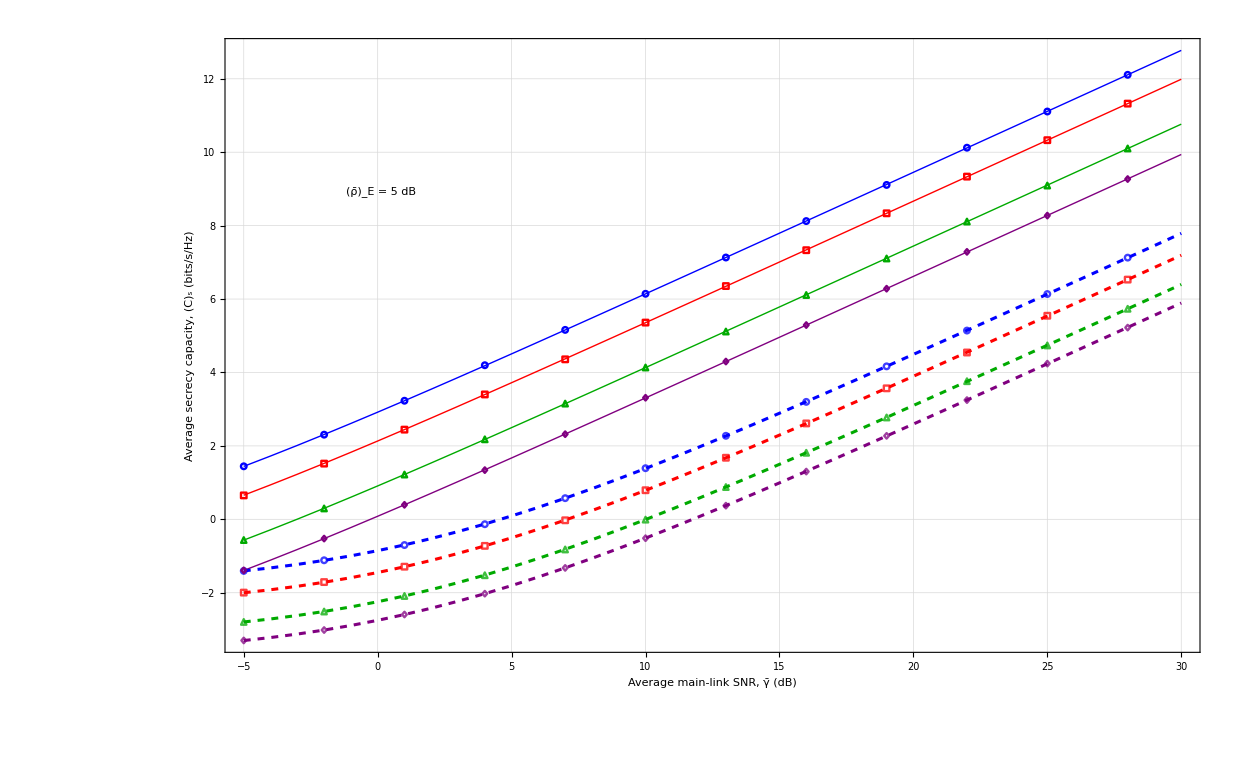

Done. Files saved directly in: G:\Thesis\Thesis done 2\Final Folder

Output files: ESMC_RIS_vs_NoRIS_FINAL_COMPARISON_LOCKED_CORES.png, ESMC_RIS_vs_NoRIS_FINAL_COMPARISON_LOCKED_CORES.pdf, CSV outputs.

```mathematica
(* ::Package::*)(*FINAL COMPARISON CODE:RIS vs No-RIS Difference-form ESMC-----------------------------------------------------------Single legitimate user+multiple eavesdroppers.Eavesdropper-only order statistics.RIS core:PATCH10 locked logic-square-root Gamma RIS SNR-positive convolution Cauchy coefficients-corrected Meijer-G kernel with 1/Sqrt[Pi]-direct term summation No-RIS core:PATCH1 locked logic-generalized-gamma SNR-positive convolution Cauchy coefficients-corrected rational-power Meijer-G argument:(m^m eta^n)/(mu^m)-direct term summation Analytical curves use ONLY closed-form/truncated analytical expressions.MC markers are ONLY for validation.NO NIntegrate,NO NSum,NO quadrature kernels.Usage:Double-click this.wl file in Mathematica and press Shift+Enter.Outputs are saved directly in the same folder as this.wl file.*)(* ============================================================*)(*0) FULL CLEAN START*)(* ============================================================*)Quiet@CloseKernels[];
ClearAll["Global`*"];
Remove["Global`*"];
ClearSystemCache[];
$HistoryLength=0;

(* ============================================================*)
(*1) OUTPUT LOCATION*)
(* ============================================================*)
codeDir=Module[{nbdir,infile},nbdir=Quiet@Check[NotebookDirectory[],$Failed];
infile=Quiet@Check[$InputFileName,""];
Which[StringQ[infile]&&StringLength[infile]>0,DirectoryName[infile],StringQ[nbdir],nbdir,True,Directory[]]];
SetDirectory[codeDir];
baseName="ESMC_RIS_vs_NoRIS_FINAL_COMPARISON_LOCKED_CORES";
Print["Saving directly beside this code file: ",codeDir];

(* ============================================================*)
(*2) SETTINGS BLOCKS*)
(* ============================================================*)

(*---Parallel settings---*)
useParallel=True;
requestedKernels=8;
If[useParallel,Quiet@CloseKernels[];
LaunchKernels[Min[requestedKernels,$ProcessorCount]];
ParallelEvaluate[$HistoryLength=0;ClearSystemCache[];];
Print["Parallel kernels active: ",Length[Kernels[]]],Print["Parallel mode disabled."]];

(*---Eavesdropper count block---*)
NeList={1,2,6,15};

(*---SNR/graph-shift block---*)
rhoEveDB=5;                  (*fixed eavesdropper average SNR in dB*)
rhoMainDBList=Range[-5,30,1];
rhoMainDBMC=Range[-5,30,3];
plotXShiftDB=0;              (*x-axis label shift only,does not change physics*)

(*---RIS fading/scale parameter block---*)
lambdaD=4;                (*destination RIS square-root Gamma shape lambda_d>0*)
lambdaE=1.3;                 (*eavesdropper RIS square-root Gamma shape lambda_e>0*)
muD=1.8;                       (*destination RIS scale multiplier mu_d>0*)
muE=0.5;                       (*eavesdropper RIS scale multiplier mu_e>0*)

(*---No-RIS fading parameter block---*)
alphaM=8/5;                  (*destination generalized-gamma alpha_m>0*)
cM=5/2;                  (*destination shape c_m>0*)
alphaH=3/2;                  (*eavesdropper generalized-gamma alpha_h>0*)
cH=3/2;                  (*eavesdropper shape c_h>0*)

(*---Optional physical SNR shifts---*)
rhoRISPhysicalShiftDB=0;
rhoNoRISPhysicalShiftDB=0;
rhoEveRISPhysicalShiftDB=0;
rhoEveNoRISPhysicalShiftDB=0;

(*---Truncation blocks---*)
KRISByNe[Ne_Integer]:=Switch[Ne,1,0,2,100,6,320,15,900,_,220];
KNoRISByNe[Ne_Integer]:=Switch[Ne,1,0,2,80,6,180,15,360,_,180];

(*---Precision/MC settings---*)
wpRIS=100;
outPrecRIS=35;
maxExtraPrecisionRIS=10000;
wpNoRIS=70;
outPrecNoRIS=45;
rationalizeTol=10^-12;
mcSamplesPerMarker=120000;
mcChunkSize=10000;
mcSeedBase=135790;

(*---Plot settings---*)
colors={Blue,Red,Darker[Green],Purple};
markerSize=0.020;            (*small hollow MC markers*)
lineThickRIS=Thick;
lineThickNoRIS=Dashed;

markerGraphics={Graphics[{EdgeForm[{Blue,AbsoluteThickness[1.7]}],FaceForm[None],Disk[]}],Graphics[{EdgeForm[{Red,AbsoluteThickness[1.7]}],FaceForm[None],Rectangle[{-1,-1},{1,1}]}],Graphics[{EdgeForm[{Darker[Green],AbsoluteThickness[1.7]}],FaceForm[None],Polygon[{{0,1.10},{-1,-1},{1,-1}}]}],Graphics[{EdgeForm[{Purple,AbsoluteThickness[1.7]}],FaceForm[None],Polygon[{{0,1.18},{1,0},{0,-1.18},{-1,0}}]}]};

(* ============================================================*)
(*3) COMMON HELPERS*)
(* ============================================================*)
rhoLinFromDB[dB_?NumericQ]:=10^(dB/10);
validNumberQ[x_]:=NumericQ[x]&&FreeQ[N[x,30],Indeterminate|ComplexInfinity|DirectedInfinity|Overflow[]];

safeNumericRISQ[x_]:=NumericQ[x]&&FreeQ[N[x,30],Indeterminate|ComplexInfinity|DirectedInfinity|Overflow[]];
realPartCleanRIS[x_]:=Module[{y},y=Quiet@Check[N[x,outPrecRIS],Indeterminate];
If[!safeNumericRISQ[y],Return[Indeterminate]];
y=Chop[Re[y],10^-22];
If[!safeNumericRISQ[y],Indeterminate,y]];

toRealNoRIS[x_,tol_:10^-25]:=Module[{y},y=Quiet@N[x,outPrecNoRIS];
Which[!NumericQ[y],Indeterminate,NumericQ[Re[y]]&&NumericQ[Im[y]]&&Abs[Im[y]]<=tol Max[1,Abs[Re[y]]],Re[y],NumericQ[y]&&Abs[Im[y]]==0,Re[y],True,Indeterminate]];

(* ============================================================*)
(*4) RIS LOCKED CORE:PATCH10*)
(* ============================================================*)

betaDRISFromDB[rhoDbarDB_]:=N[rhoLinFromDB[rhoDbarDB+rhoRISPhysicalShiftDB]*muD,wpRIS];
betaERISFixed:=N[rhoLinFromDB[rhoEveDB+rhoEveRISPhysicalShiftDB]*muE,wpRIS];

ClearAll[RISLKernelMeijerGClosed];
RISLKernelMeijerGClosed[aIn_,muIn_,betaIn_]:=RISLKernelMeijerGClosed[aIn,muIn,betaIn]=Block[{$MaxExtraPrecision=maxExtraPrecisionRIS},Module[{a,mu,beta,z,raw,epsList,probes,good,val},a=SetPrecision[N[aIn,wpRIS],wpRIS];
mu=SetPrecision[N[muIn,wpRIS],wpRIS];
beta=SetPrecision[N[betaIn,wpRIS],wpRIS];
z=SetPrecision[4 beta/mu^2,wpRIS];
raw=Quiet@Check[N[(2^(a-1)/(Sqrt[Pi] mu^a))*MeijerG[{{1,1,(1-a)/2,1-a/2},{}},{{1},{0}},z],wpRIS],Indeterminate];
val=realPartCleanRIS[raw];
If[safeNumericRISQ[val]&&val>0,Return[val]];
epsList=SetPrecision[{10^-8,-10^-8,3*10^-8,-3*10^-8,10^-7,-10^-7},wpRIS];
probes=Quiet@Table[Check[N[(2^(a+eps-1)/(Sqrt[Pi] mu^(a+eps)))*MeijerG[{{1,1,(1-(a+eps))/2,1-(a+eps)/2},{}},{{1},{0}},z],wpRIS],Indeterminate],{eps,epsList}];
good=Select[realPartCleanRIS/@probes,safeNumericRISQ[#]&&#>0&];
If[Length[good]>=2,Return[N[Median[good],outPrecRIS]]];
Print["WARNING: RIS kernel failed at a=",aIn,", mu=",muIn,", beta=",N[betaIn,8]];
Indeterminate]];

ClearAll[RISCauchyCoeffsPositive];
RISCauchyCoeffsPositive[lambda_,m_Integer,K_Integer]:=RISCauchyCoeffsPositive[lambda,m,K]=Module[{f,h,newh,r,n,j},If[m==0,Return[Join[{SetPrecision[1,wpRIS]},ConstantArray[SetPrecision[0,wpRIS],K]]]];
f=Table[SetPrecision[1/Gamma[lambda+k+1],wpRIS],{k,0,K}];
h=Join[{SetPrecision[1,wpRIS]},ConstantArray[SetPrecision[0,wpRIS],K]];
For[r=1,r<=m,r++,newh=Table[N[Sum[h[[j+1]] f[[n-j+1]],{j,0,n}],wpRIS],{n,0,K}];
h=newh;];
h];

ClearAll[RISCeRowsForNe];
RISCeRowsForNe[Ne_Integer,betaE_]:=Module[{K,A,rows},K=KRISByNe[Ne];
A=RISCauchyCoeffsPositive[lambdaE,Ne-1,K];
rows=Table[Module[{a,an,L,term},a=N[Ne lambdaE+n,wpRIS];
an=N[A[[n+1]],wpRIS];
L=RISLKernelMeijerGClosed[a,Ne,betaE];
term=If[safeNumericRISQ[L]&&safeNumericRISQ[an],N[an*L,wpRIS],Indeterminate];
{Ne,n,N[an,22],N[L,22],N[term,22]}],{n,0,K}];
rows];

ClearAll[RISCeBitsDirect];
RISCeBitsDirect[Ne_Integer,betaE_]:=Module[{rows,terms,sumTerms,ce},rows=RISCeRowsForNe[Ne,betaE];
terms=rows[[All,5]];
sumTerms=Fold[Plus,SetPrecision[0,wpRIS],Select[terms,safeNumericRISQ[#]&]];
ce=N[(Ne/Gamma[lambdaE]) sumTerms/Log[2],outPrecRIS];
{ce,rows}];

ClearAll[RISCdBits];
RISCdBits[betaD_]:=Module[{L},L=RISLKernelMeijerGClosed[lambdaD,1,betaD];
N[L/Gamma[lambdaD]/Log[2],outPrecRIS]];

ClearAll[RISMCESMCChunked];
RISMCESMCChunked[Ne_Integer,rhoDbarDB_,seed_Integer]:=Module[{betaD,betaE,done=0,total=0.,take,u,vmax,vals},betaD=N[rhoLinFromDB[rhoDbarDB+rhoRISPhysicalShiftDB]*muD];
betaE=N[rhoLinFromDB[rhoEveDB+rhoEveRISPhysicalShiftDB]*muE];
SeedRandom[seed];
While[done<mcSamplesPerMarker,take=Min[mcChunkSize,mcSamplesPerMarker-done];
u=RandomVariate[GammaDistribution[N[lambdaD],1],take];
gammaD=betaD u^2;
vmax=If[Ne==1,RandomVariate[GammaDistribution[N[lambdaE],1],take],Max/@RandomVariate[GammaDistribution[N[lambdaE],1],{take,Ne}]];
vals=Log2[1+gammaD]-Log2[1+betaE vmax^2];
total+=Total[vals];
done+=take;];
N[total/mcSamplesPerMarker,12]];

(* ============================================================*)
(*5) No-RIS LOCKED CORE:PATCH1*)
(* ============================================================*)

ClearAll[convTruncPositiveNR,NRCauchyCoeffsPositive];
convTruncPositiveNR[x_List,y_List,K_Integer]:=Module[{lx=Length[x],ly=Length[y]},Table[Sum[If[i+1<=lx&&r-i+1<=ly,x[[i+1]] y[[r-i+1]],0],{i,0,r}],{r,0,K}]];

NRCauchyCoeffsPositive[ch_,power_Integer,K_Integer,wp_:70]:=Module[{q,h,rep},If[power==0,Return[Join[{N[1,wp]},ConstantArray[N[0,wp],K]]]];
q=Table[N[1/Gamma[ch+k+1],wp],{k,0,K}];
h={N[1,wp]};
Do[h=convTruncPositiveNR[h,q,K],{rep,1,power}];
N[h,wp]];

ClearAll[NRLogKernelMeijerGeneral];
NRLogKernelMeijerGeneral[aIn_,muIn_,etaIn_,alphaIn_,wp_:70]:=Module[{pRat,m,n,a,mu,eta,Ablock,Bblock,Cblock,Dblock,upper,arg,pref,val,upperBound,out},pRat=Rationalize[2/alphaIn,rationalizeTol];
m=Numerator[pRat];
n=Denominator[pRat];
a=SetPrecision[aIn,wp];
mu=SetPrecision[muIn,wp];
eta=SetPrecision[etaIn,wp];
Ablock=Table[1-j/n,{j,0,n-1}];
Bblock=Table[1-(a+k)/m,{k,0,m-1}];
Cblock=Table[(j+1)/n,{j,0,n-1}];
Dblock=Table[1-(j+1)/n,{j,0,n-1}];
upper=Join[Ablock,Ablock,Bblock];
(*PATCH1 locked argument:no n^n denominator.*)arg=N[(m^m eta^n)/(mu^m),wp];
pref=N[((2 Pi)^(1-n+(1-m)/2)*m^(a-1/2))/(mu^a),wp];
val=Quiet@Check[pref*N[MeijerG[{upper,{}},{Cblock,Dblock},arg],wp],Indeterminate];
out=toRealNoRIS[val];
upperBound=Quiet@Check[N[(Gamma[a]/mu^a)*Log[1+eta*mu^(-pRat)*Gamma[a+pRat]/Gamma[a]],wp],Infinity];
upperBound=toRealNoRIS[upperBound];
If[validNumberQ[out]&&out>0&&(!validNumberQ[upperBound]||out<=5 Max[1,upperBound]),N[out,outPrecNoRIS],Indeterminate]];

ClearAll[NRMainCapacityBits];
NRMainCapacityBits[rhoMDB_?NumericQ]:=Module[{rhoMlin,etaM,L,Cm},rhoMlin=rhoLinFromDB[rhoMDB+rhoNoRISPhysicalShiftDB];
etaM=rhoMlin/(cM^(2/alphaM));
L=NRLogKernelMeijerGeneral[cM,1,etaM,alphaM,wpNoRIS];
If[!validNumberQ[L],Return[Indeterminate]];
Cm=L/Gamma[cM]/Log[2];
N[Cm,outPrecNoRIS]];

ClearAll[NREaveCapacityBits];
NREaveCapacityBits[Ne_Integer]:=Module[{rhoHlin,etaH,K,A,terms,Ce,pH},rhoHlin=rhoLinFromDB[rhoEveDB+rhoEveNoRISPhysicalShiftDB];
pH=2/alphaH;
etaH=rhoHlin/(cH^pH);
K=KNoRISByNe[Ne];
A=NRCauchyCoeffsPositive[cH,Ne-1,K,wpNoRIS];
terms=Table[With[{coeff=A[[n+1]],L=NRLogKernelMeijerGeneral[Ne*cH+n,Ne,etaH,alphaH,wpNoRIS]},If[validNumberQ[L],coeff*L,Indeterminate]],{n,0,K}];
If[Count[terms,_?(Not@*validNumberQ)]>0,Print["WARNING: invalid No-RIS kernel terms for Ne=",Ne,". Count = ",Count[terms,_?(Not@*validNumberQ)]];];
terms=Select[terms,validNumberQ];
Ce=(Ne/Gamma[cH]) Total[terms]/Log[2];
N[Ce,outPrecNoRIS]];

ClearAll[NRMCESMCChunked];
NRMCESMCChunked[rhoMDB_?NumericQ,Ne_Integer,seed_Integer]:=Module[{remaining=mcSamplesPerMarker,sumM=0.,sumE=0.,take,Zm,Zh,gammaM,gammaEmax,rhoMlin,rhoHlin},SeedRandom[seed];
rhoMlin=rhoLinFromDB[rhoMDB+rhoNoRISPhysicalShiftDB];
rhoHlin=rhoLinFromDB[rhoEveDB+rhoEveNoRISPhysicalShiftDB];
While[remaining>0,take=Min[mcChunkSize,remaining];
Zm=RandomVariate[GammaDistribution[N[cM],1],take];
gammaM=rhoMlin*(Zm/N[cM])^(2/N[alphaM]);
If[Ne==1,Zh=RandomVariate[GammaDistribution[N[cH],1],take];
gammaEmax=rhoHlin*(Zh/N[cH])^(2/N[alphaH]),Zh=RandomVariate[GammaDistribution[N[cH],1],{take,Ne}];
gammaEmax=rhoHlin*(Max/@Zh/N[cH])^(2/N[alphaH])];
sumM+=Total[Log[2,1+gammaM]];
sumE+=Total[Log[2,1+gammaEmax]];
remaining-=take;];
N[(sumM-sumE)/mcSamplesPerMarker,12]];

(* ============================================================*)
(*6) COMPUTE RIS AND No-RIS ANALYTICAL TERMS*)
(* ============================================================*)

Print["Computing RIS Ce,max from PATCH10 locked core..."];
betaERIS=betaERISFixed;
risCePackages=Table[Module[{pack=RISCeBitsDirect[Ne,betaERIS]},{Ne,KRISByNe[Ne],pack[[1]],pack[[2]]}],{Ne,NeList}];
risCeDiagRows=Table[Module[{Ne=risCePackages[[i,1]],K=risCePackages[[i,2]],ce=risCePackages[[i,3]],rows=risCePackages[[i,4]],terms,totalAbs,tailAbs,ratio,bad},terms=rows[[All,5]];
totalAbs=Total[Abs/@Select[terms,safeNumericRISQ[#]&]];
tailAbs=Total[Abs/@Select[Take[terms,-Min[25,Length[terms]]],safeNumericRISQ[#]&]];
ratio=If[totalAbs==0,Indeterminate,N[tailAbs/totalAbs,12]];
bad=Count[terms,_?(Not@*safeNumericRISQ)];
{Ne,K,ce,ratio,bad}],{i,Length[risCePackages]}];
Print["RIS Ce diagnostics {Ne,K,CeBits,Last25Ratio,BadTerms}: ",risCeDiagRows];

Print["Computing No-RIS Ce,max from PATCH1 locked core..."];
nrCeTable=Table[{Ne,KNoRISByNe[Ne],NREaveCapacityBits[Ne]},{Ne,NeList}];
Print["No-RIS Ce diagnostics {Ne,K,CeBits}: ",nrCeTable];

Print["Computing analytical comparison curves..."];
risAnalyticalRows=Flatten[Table[Module[{ce=risCePackages[[i,3]],betaD,cd,esmc},betaD=betaDRISFromDB[rhoDB];
cd=RISCdBits[betaD];
esmc=N[cd-ce,outPrecRIS];
{"RIS","CF",risCePackages[[i,1]],rhoDB+plotXShiftDB,rhoDB,esmc}],{i,Length[risCePackages]},{rhoDB,rhoMainDBList}],1];

nrAnalyticalRows=Flatten[Table[Module[{ce=SelectFirst[nrCeTable,#[[1]]==Ne&][[3]],cd,esmc},cd=NRMainCapacityBits[rhoDB];
esmc=N[cd-ce,outPrecNoRIS];
{"NoRIS","CF",Ne,rhoDB+plotXShiftDB,rhoDB,esmc}],{Ne,NeList},{rhoDB,rhoMainDBList}],1];

analyticalRows=Join[risAnalyticalRows,nrAnalyticalRows];
analyticalRows=Select[analyticalRows,validNumberQ[#[[6]]]&];

(* ============================================================*)
(*7) MONTE CARLO MARKERS*)
(* ============================================================*)
If[useParallel&&Length[Kernels[]]>0,DistributeDefinitions[RISMCESMCChunked,NRMCESMCChunked,rhoLinFromDB,lambdaD,lambdaE,muD,muE,alphaM,cM,alphaH,cH,rhoEveDB,rhoRISPhysicalShiftDB,rhoNoRISPhysicalShiftDB,rhoEveRISPhysicalShiftDB,rhoEveNoRISPhysicalShiftDB,mcSamplesPerMarker,mcChunkSize,mcSeedBase,NeList,rhoMainDBMC,plotXShiftDB];];

Print["Computing small hollow MC validation markers..."];
risMCRows=If[useParallel&&Length[Kernels[]]>0,Flatten[ParallelTable[{"RIS","MC",Ne,rhoDB+plotXShiftDB,rhoDB,RISMCESMCChunked[Ne,rhoDB,mcSeedBase+1000 Ne+Round[10 (rhoDB+100)]]},{Ne,NeList},{rhoDB,rhoMainDBMC}],1],Flatten[Table[{"RIS","MC",Ne,rhoDB+plotXShiftDB,rhoDB,RISMCESMCChunked[Ne,rhoDB,mcSeedBase+1000 Ne+Round[10 (rhoDB+100)]]},{Ne,NeList},{rhoDB,rhoMainDBMC}],1]];

nrMCRows=If[useParallel&&Length[Kernels[]]>0,Flatten[ParallelTable[{"NoRIS","MC",Ne,rhoDB+plotXShiftDB,rhoDB,NRMCESMCChunked[rhoDB,Ne,mcSeedBase+20000+1000 Ne+Round[10 (rhoDB+100)]]},{Ne,NeList},{rhoDB,rhoMainDBMC}],1],Flatten[Table[{"NoRIS","MC",Ne,rhoDB+plotXShiftDB,rhoDB,NRMCESMCChunked[rhoDB,Ne,mcSeedBase+20000+1000 Ne+Round[10 (rhoDB+100)]]},{Ne,NeList},{rhoDB,rhoMainDBMC}],1]];
mcRows=Join[risMCRows,nrMCRows];

(* ============================================================*)
(*8) ERROR AND SANITY CHECKS*)
(* ============================================================*)
cfValueAt[scenario_,Ne_,rhoDB_]:=Module[{row},row=SelectFirst[analyticalRows,#[[1]]==scenario&&#[[3]]==Ne&&#[[5]]==rhoDB&,Missing["NoCF"]];
If[ListQ[row],row[[6]],Missing["NoCF"]]];

errorRows=Table[Module[{cf=cfValueAt[row[[1]],row[[3]],row[[5]]],err},err=If[NumberQ[cf],Abs[cf-row[[6]]],Missing["NoCF"]];
{row[[1]],row[[3]],row[[4]],row[[5]],cf,row[[6]],err}],{row,mcRows}];

Print["Max absolute CF-MC error = ",Max[Cases[errorRows[[All,7]],_?NumericQ]]," bits/s/Hz"];
lastSNR=Last[rhoMainDBList];
risLastVals=Table[cfValueAt["RIS",Ne,lastSNR],{Ne,NeList}];
nrLastVals=Table[cfValueAt["NoRIS",Ne,lastSNR],{Ne,NeList}];
Print["RIS ESMC at ",lastSNR," dB: ",Transpose[{NeList,risLastVals}]];
Print["No-RIS ESMC at ",lastSNR," dB: ",Transpose[{NeList,nrLastVals}]];
If[And@@Thread[Differences[risLastVals]<0],Print["PASS: RIS ESMC decreases with Ne."],Print["WARNING: RIS ESMC ordering failed."]];
If[And@@Thread[Differences[nrLastVals]<0],Print["PASS: No-RIS ESMC decreases with Ne."],Print["WARNING: No-RIS ESMC ordering failed."]];

(* ============================================================*)
(*9) SINGLE COMPARISON PLOT*)
(* ============================================================*)

xAxisLabel="Average main-link SNR, \!\(\*OverscriptBox[\(γ\), \(_\)]\) (dB)";
yAxisLabel="Average secrecy capacity, \!\(\*SubscriptBox[OverscriptBox[\(C\), \(_\)], \(s\)]\) (bits/s/Hz)";

risCFData=Table[({#[[4]],#[[6]]}&/@Select[analyticalRows,#[[1]]=="RIS"&&#[[3]]==Ne&]),{Ne,NeList}];
nrCFData=Table[({#[[4]],#[[6]]}&/@Select[analyticalRows,#[[1]]=="NoRIS"&&#[[3]]==Ne&]),{Ne,NeList}];
risMCData=Table[({#[[4]],#[[6]]}&/@Select[mcRows,#[[1]]=="RIS"&&#[[3]]==Ne&]),{Ne,NeList}];
nrMCData=Table[({#[[4]],#[[6]]}&/@Select[mcRows,#[[1]]=="NoRIS"&&#[[3]]==Ne&]),{Ne,NeList}];

risCFPlot=ListLinePlot[risCFData,PlotStyle->(Directive[#,lineThickRIS]&/@colors),InterpolationOrder->1];

nrCFPlot=ListLinePlot[nrCFData,PlotStyle->(Directive[#,lineThickNoRIS,AbsoluteThickness[2.2]]&/@colors),InterpolationOrder->1];

risMCPlot=ListPlot[risMCData,PlotStyle->(Directive[#,PointSize[0.010]]&/@colors),PlotMarkers->Table[{markerGraphics[[i]],markerSize},{i,Length[NeList]}]];

nrMCPlot=ListPlot[nrMCData,PlotStyle->(Directive[#,PointSize[0.009],Opacity[0.75]]&/@colors),PlotMarkers->Table[{markerGraphics[[i]],markerSize*0.78},{i,Length[NeList]}]];

lineLegend=LineLegend[Join[colors,colors],Join[("RIS, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[#]&/@NeList),("Without-RIS, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[#]&/@NeList)],LegendMarkers->Join[ConstantArray[None,Length[NeList]],ConstantArray[None,Length[NeList]]],LabelStyle->{FontFamily->"Times New Roman",FontSize->13,Black},LegendFunction->"Frame",LegendLayout->"Column"];

markerLegend=PointLegend[colors,("MC, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[#]&/@NeList),LegendMarkers->markerGraphics,LabelStyle->{FontFamily->"Times New Roman",FontSize->13,Black},LegendFunction->"Frame",LegendLayout->"Column"];

paramLabel=Style["  \!\(\*SubscriptBox[OverscriptBox[\(ρ\), \(_\)], \(E\)]\) = 5 dB",FontFamily->"Times New Roman",FontSize->13,Bold,Black];

comparisonFig=Legended[Show[risCFPlot,nrCFPlot,risMCPlot,nrMCPlot,Frame->True,FrameTicksStyle->Directive[Black,13,FontFamily->"Times New Roman"],GridLines->Automatic,ImageSize->1250,PlotRange->All,FrameLabel->{Style[xAxisLabel,16,Black,FontFamily->"Times New Roman"],Style[yAxisLabel,16,Black,FontFamily->"Times New Roman"]},PlotLabel->None,BaseStyle->{FontFamily->"Times New Roman",FontSize->13}],Placed[Column[{lineLegend,markerLegend,paramLabel},Spacings->0.4],{0.16,0.75}]];

Print[comparisonFig];

(* ============================================================*)
(*10) EXPORTS-SAME FOLDER AS CODE*)
(* ============================================================*)
Export[FileNameJoin[{codeDir,baseName<>".png"}],comparisonFig,ImageResolution->300];
Export[FileNameJoin[{codeDir,baseName<>".pdf"}],comparisonFig];
Export[FileNameJoin[{codeDir,"ESMC_Comparison_CF_Data.csv"}],Prepend[analyticalRows,{"Scenario","Type","Ne","rhoPlotDB","rhoPhysicalDB","ESMC_CF"}]];
Export[FileNameJoin[{codeDir,"ESMC_Comparison_MC_Markers.csv"}],Prepend[mcRows,{"Scenario","Type","Ne","rhoPlotDB","rhoPhysicalDB","ESMC_MC"}]];
Export[FileNameJoin[{codeDir,"ESMC_Comparison_Error.csv"}],Prepend[errorRows,{"Scenario","Ne","rhoPlotDB","rhoPhysicalDB","CF","MC","AbsError"}]];
Export[FileNameJoin[{codeDir,"RIS_ESMC_CeDiagnostics_Comparison.csv"}],Prepend[risCeDiagRows,{"Ne","K","CeBits","Last25Ratio","BadTerms"}]];
Export[FileNameJoin[{codeDir,"NoRIS_ESMC_CeDiagnostics_Comparison.csv"}],Prepend[nrCeTable,{"Ne","K","CeBits"}]];

Print["Done. Files saved directly in: ",codeDir];
Print["Output files: ",baseName<>".png, ",baseName<>".pdf, CSV outputs."];

If[useParallel,Quiet@CloseKernels[]];
```